# Lista II - Física Matemática 1

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.Sousa@usp.br

## 2.a)

#### COnsiderado uma partícula quântica confinada num poço de potencial, região onde x ∈ [0,L], temos que esse tipo de sistema é descrito por uma função ψ(x), chamada de função de onda, que satisfaz -ℏ^2/(2m) (d^2 ψ)/dx^2 =Eψ(x) (2.1). Mostraremos que sendo ψ(x) = ASin[kx] + BCos[kx](2.2), A, B e k são constantes, então, E = (-ℏ^2 k^2)/(2m) Primeiro derivarei ψ(x): →ψ’(x) = AkCos[kx] - BkSin[kx] (2.3) →ψ”(x) = -k^2 ASin[kx] -k^2 BCos[kx] = -k^2ψ(x) (2.4) Substituindo o resultado da Eq.(2.4) na Eq.(2.1) , temos: -ℏ^2/(2m) (d^2 ψ)/dx^2 =Eψ ⇔ -ℏ^2/(2m) -k^2ψ(x)=Eψ(x) ⇔ E = (ℏ^2 k^2)/(2m) (2.5)

## 2.b)

#### Mostraremos que dadas as condições de contorno ψ(0) = ψ(L) = 0, a Eq.(2.2) será satisfeita para B = 0 e se k for discreto, de forma que k = πn/L(2.6), n = 1, 2... ψ(0) = ASin[0] + BCos[0] = B = 0 (2.7), levando em consideração que B = 0. ψ(L) = ASin[kL] + BCos[kL] = ASin[kL] = 0 (2.8), com isso teremos que: Sin[kL] = 0 ⇔ kL = Sin^-1[0] = nπ. Por fim, temos que: k = nπ/L

## 2.c)

#### Encontrando um A que satisfaça a solução: ∫_0^L |ψ(x)|.b2ⅆx=1 (2.9). Para isso temos que, |ψ(x)|.b2 = A.b2sin.b2(nℼ/L x) (2.10). Com isso fazemos, A.b2∫_0^L sin.b2(nℼ/L x)ⅆx= (A.b2[x/2 -(sin((2 nℼ)/L x)L)/(4nℼ)])_0^L= A.b2[L/2 -(sin(2 nℼ)L)/(4nℼ)]=1, como para todo n inteiro sin(2nℼ)=0 (2.11). Temos que por fim que: A = (√2)/(√L)(2.12)

## 3.a)

#### Considerando a equação não-linear de primeira ordem, chamada de Equação de Bernoulli: y' + P(x)y = Q(x)y^n (3.1), sendo n um número arbitrário, podemos reagrupar a equação da seguinte maneira: y'/y^n + (P(x)y)/y^n = Q(x) (3.2), sendo Z = y^(1-n) (3.3), o que implica que a sua derivada é dada por: Z' = (1-n)y^-n y'(3.4), substituímos a Eq.(3.3) e Eq.(3.4) em Eq.(3.1): y' y^-n + P(x)y^(1-n) = Q(x) → Z'/(1-n)+ P(x)Z=Q(x) → Z'+(1-n)P(x)Z = (1-n)Q(x) (3.5)

## 3.b)

#### Como já vimos em sala, a solução da EDO linear não homogênea: y' + α(x)y = β(x) (3.6), possui o seguinte formato: y(x) = Cℯ^(-I(x)) + ℯ^(-I(x))∫β(x)ℯ^(I(x))ⅆx (3.7), sendo I(x) = ∫α(x)ⅆx (3.8) (nosso fator integrante). Adaptando para o nosso caso temos: Z(x) = Cℯ^(-∫(1-n)P(x)ⅆx) + ℯ^(-∫(1-n)P(x)ⅆx) ∫(1-n)Q(x)e^(∫(1-n)P(x)ⅆx)ⅆx (3.9) Por fim, temos que a solução de y é: y(x) = Z^(1/(1-n)) (3.10)

## 3.c)

#### Aplicando os conhecimentos anteriores para a resolução da EDO: 3xy.b2y' + 3y.b3 = 1 (3.11) → y.b2y' + y.b3 1/x = 1/(3x) (3.12) → Z = y.b3 (3.13) → Z' = 3y.b2y' (3.14) Z'/3 + Z 1/x = 1/(3x) (3.15) → Z' + 3/x Z = 1/x (3.16) Podemos resolver a integral do jeito citado no item b, porém existe uma maneira mais simples. Z' + 3/x Z = 1/x(3.17) → Z'(x) = 1/x(1-3Z(x)) (3.18)→(Z'(x))/(1-3Z(x))=1/x (3.19), supondo 1 - 3Z(x) ≠ 0 e sendo u = 1-3Z ⇒ du =-3dZ, temos: (ⅆZ/ⅆx)/(1-3Z(x))=1/x (3.20) → ∫ⅆZ/(1-3Z(x))=∫ⅆx/x (3.21)→ - 1/3∫ⅆu/u= ∫ⅆx/x (3.22) →-1/3Log(u)=Log(x) (3.23) → -1/3Log(1-3Z) = Log(x) + C (3.24) → Log(1-3Z) = -3Log(x) + C (3.25) → 1-3Z = C/(x.b3) (3.26) → Z = 1/3 + c/(X.b3) (3.27) Por fim, teremos que y(x) = (Z(x))^(1/3)= (1/3 + c/(X.b3))^(1/3) =(x.b3 + C)^(1/3)/(3^(1/3)x) (3.28)

## 4.a)

#### Sendo o modelo da evolução de uma população y(t) de uma certa espécie dado por: ⅆy/ⅆt= ry(1-y/k) (4.1), sendo y e k constantes. Usaremos os resultados do item anterior para encontrar a solução de y(t), já que a Eq. se enquadra como uma equação de Bernoulli, onde temos a seguinte condição inicial y(t=0) = y_0 (4.2). ⅆy/ⅆt= ry(1-y/k) (4.3)→ y'= ry - r/k y.b2(4.4)→ y'-ry=-r/ky.b2(4.5) → y'/(y.b2)+ -r/y =-r/k (4.6)→ y' y^-2-ry^-1=-r/k(4.7), sendo Z = -y^-1 (4.8)e suas derivada Z'=y^-2 y' (4.9). Temos então que a Eq.(4.1) terá o seguinte formato: Z' + rZ =-r/k (4.10) →Encontrando o nosso fator integrante: I(t') = ∫_0^t rⅆt⇒I(t) - I(0)= rt (4.11). Nesse ponto é legal lembrarmos que dado Eq.(4.2) e a Eq.(4.8) temos que Z(0) = - 1/y_0(4.12) Por uma adaptação da Eq.(3.9), que vimos em sala, temos que: Z(t) = Z(0)ℯ^-rt + ℯ^-rt∫_0^t (-r/k)ℯ^rt' ⅆt' = -1/y_0 ℯ^-rt -ℯ^-rt/k ℯ^rt'|_0^t= Z(t) = -1/y_0 ℯ^-rt -ℯ^-rt/k[ℯ^rt-1] ⇒ Z(t) = -1/y_0 ℯ^-rt -1/k +ℯ^-rt/k Z(t) = ( -1/y_0+1/k)ℯ^-rt -1/k (4.13) Com isso, temos que a solução y(t) será dada por: y(t) = -1/Z(4.14) Por fim, temos que y(t) = k/(1 - k( -1/y_0 + 1/k)ℯ^-rt)=k/(1 +( k/y_0 -1)ℯ^-rt) (4.15)

## 4.b)

#### Considerando y_0 e k constantes positivas, x = rt = tempo adimensional e y/k a medida adimensional da população. Ao plotarmos a função y(t) =k/(1 +( k/y_0 -1)ℯ^-rt) , podemos analisar que quando y_0>k teremos uma função decrescente e quando y_0<k teremos uma função crescente. No entanto depois de um tempo ambas as funções convergem para o valor de k.

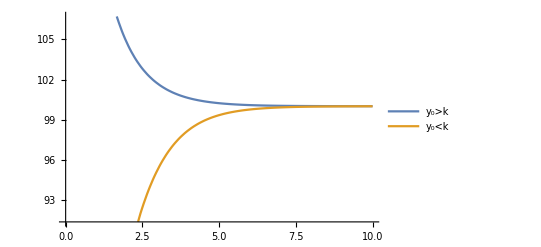

```mathematica
(*Defino k = 100, plotarei dois gráfico o "y_0>k" para Subscript[y, 0]=150 (onde ( k/Subscript[y, 0] -1)=-1/3 )  e o "y_0<k" para Subscript[y, 0]=50 (onde ( k/Subscript[y, 0] -1)=1 ).*)


Plot[ {100/(1 -1/3*Exp[-x]),100/(1 +1*Exp[-x])},{x, 0, 10},PlotLegends->{"y_0>k", "y_0<k"}]
```

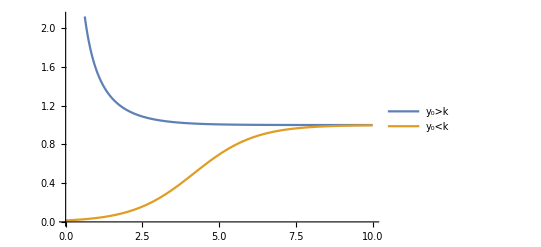

```mathematica
(*Defino k = 1, plotarei dois gráfico o "y_0>k" para Subscript[y, 0]=66 (onde ( k/Subscript[y, 0] -1)=-65/66 )  e o "y_0<k" para Subscript[y, 0]=1/66 (onde ( k/Subscript[y, 0] -1)=65 ).*)


Plot[ {1/(1 -65/66*Exp[-x]),1/(1 +65*Exp[-x])},{x, 0, 10},PlotLegends->{"y_0>k", "y_0<k"}]
```

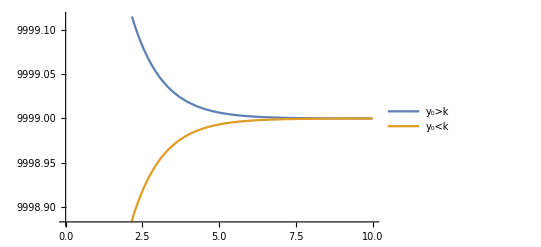

```mathematica
(*Defino k = 9999, plotarei dois gráfico o "y_0>k" para Subscript[y, 0]=10000 (onde ( k/Subscript[y, 0] -1)=-1/10000 )  e o "y_0<k" para Subscript[y, 0]=9998 (onde ( k/Subscript[y, 0] -1)=1/9998 ).*)


Plot[ {9999/(1 -1/10000*Exp[-x]),9999/(1 +1/9998*Exp[-x])},{x, 0, 10},PlotLegends->{"y_0>k", "y_0<k"}]
```

## 5.a)

#### Para encontrar a solução da EDO R ⅆQ/ⅆt+ Q/C= V(t)(5.1), com a condição inicial Q(0)=0 (5.2), primeiro devemos expandir a tensão V(t)= Piecewise[{{V_0, 0<t<ℼ/ω}, {-V_0, -ℼ<t<0}}] (5.3)em série de Fourier. Serei bem simples no desenvolvimento da série de Fourier. →V(t) terá o seguinte formato: V(t) =∑_(n∈ℤ) c_n ℯ^ⅈωnt (5.4), c_n= 1/T∫_(-T/2)^(T/2) V(t)ℯ^-ⅈωnt ⅆt= ω/(2ℼ)[-∫_(-T/2)^0 V_0 ℯ^-ⅈωnt ⅆt+∫_0^(T/2) V_0 ℯ^-ⅈωnt ⅆt] v_0/(2ℼnⅈ)[ℯ^-ⅈωnt|_(-ℼ/ω)^0 -ℯ^-ⅈωnt|_0^(ℼ/ω)]= v_0/(2ℼnⅈ)[1-ℯ^-ⅈℼn-ℯ^-ⅈℼn+1]=v_0/ℼnⅈ[1- (-1)^n] Com isso, V(t) =∑_(n∈ℤ) [v_0/Rℼnⅈ[1- (-1)^n]]ℯ^ⅈωnt(5.5) Assim, nossa EDO será: ⅆQ/ⅆt+ Q/RC=∑_(n∈ℤ) [v_0/ℼnⅈ[1- (-1)^n]]ℯ^ⅈωnt(5.6) A solução de Q(t) pode ser obtida pela pelo método do fator de integração, como vimos em aula e citamos nas outras questões: Q(t) = Q(0)ℯ^(-∫_0^t 1/RCⅆt) + ℯ^(-∫1/RCⅆt)∫_0^t ∑_(n∈ℤ) [v_0/Rℼnⅈ[1- (-1)^n]]ℯ^ⅈωnt ℯ^(∫1/RCⅆt)ⅆt Q(t) = ℯ^(-t/RC)∑_(n∈ℤ) [v_0/Rℼnⅈ[1- (-1)^n]]∫_0^t ℯ^((1/RC+ⅈωn)t)ⅆt Q(t) = ℯ^(-t/RC)∑_(n∈ℤ) [v_0/Rℼnⅈ[1- (-1)^n]/(1/RC+ⅈωn)][ℯ^((1/RC+ⅈωn)t)-1] Q(t) = ∑_(n∈ℤ) [v_0/Rℼn[1- (-1)^n]/(ⅈ/RC-ωn)][ℯ^ⅈωnt-ℯ^(-t/RC)] (5.7) Posso simplificar ainda mais a solução Q(t), considerando essa somatório em um novo conjunto 𝕊 = {s: s = 2n +1, n ∈ ℤ} (5.8) Q(t) = v_0/Rℼ∑_(s∈𝕊) [2/(ⅈs/RC-ωs.b2)][ℯ^ⅈωst-ℯ^(-t/RC)] (5.9)

## 5.b)

#### Plotaremos a função (Q(t)ωR)/V_0=1/ℼ∑_(s∈𝕊) [2/(ⅈωs/RC-s.b2)][ℯ^ⅈωst-ℯ^(-t/RC)] (5.10), que corresponde a uma carga adimensional. Simplificaremos essa função colocando ω = 1 e α = 1/RC. Com isso temos que: (Q(t)R)/V_0=1/ℼ∑_(s∈𝕊) [2/(ⅈsα-s.b2)][ℯ^ⅈst-ℯ^-αt] (5.11) . A seguir veremos alguns exemplos de plots para diferentes valores de α, onde usaremos um truquezinho de sempre começar de a soma por um numero ímpar negativo e terminar no seu simétrico positivo, para que todas as contribuições imaginarias sejam canceladas. Além disso, nosso passo da soma será de dois em dois para que o nosso s não passe por 0. Já podemos adiantar que nos plots observamos que quanto maior for o valor de α, mais próximo da onda quadrada estaremos, e quando menor o valor de α, mais proximo da onda triangular estaremos.

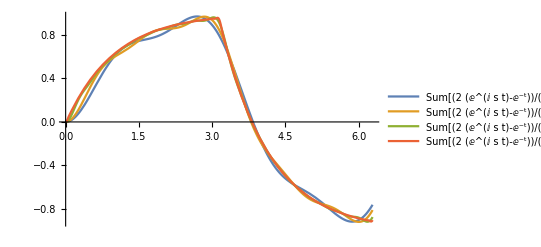

```mathematica
(*Para α = 1*)
Plot[{Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-3,3,2}],Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-5,5,2}],Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-15,15,2}],Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-55,55,2}]}, {t,0,2π},PlotLegends->"Expressions"]
```

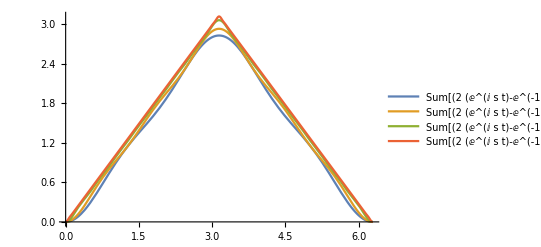

```mathematica
(*Para α = 0.000001*)
Plot[{Sum[(2*(E^(ⅈ s t)-E^(-0.000001*t)))/(π*(ⅈ*0.000001*s  - s^2)), {s,-3,3,2}],Sum[(2*(E^(ⅈ s t)-E^(-0.000001*t)))/(π*(ⅈ*0.000001*s  - s^2)), {s,-5,5,2}],Sum[(2*(E^(ⅈ s t)-E^(-0.000001*t)))/(π*(ⅈ*0.000001*s  - s^2)), {s,-15,15,2}],Sum[(2*(E^(ⅈ s t)-E^(-0.000001*t)))/(π*(ⅈ*0.000001*s  - s^2)), {s,-55,55,2}]}, {t,0,2π},PlotLegends->"Expressions"]
```

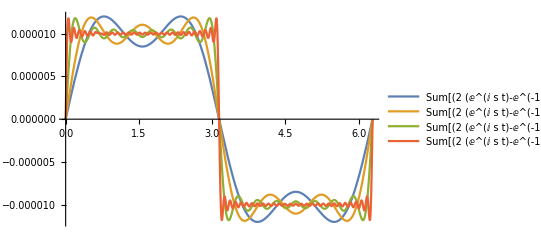

```mathematica
(*Para α = 100000*)
Plot[{Sum[(2*(E^(ⅈ s t)-E^(-100000*t)))/(π*(ⅈ*100000*s  - s^2)), {s,-3,3,2}],Sum[(2*(E^(ⅈ s t)-E^(-100000*t)))/(π*(ⅈ*100000*s  - s^2)), {s,-5,5,2}],Sum[(2*(E^(ⅈ s t)-E^(-100000*t)))/(π*(ⅈ*100000*s  - s^2)), {s,-15,15,2}],Sum[(2*(E^(ⅈ s t)-E^(-100000*t)))/(π*(ⅈ*100000*s  - s^2)), {s,-55,55,2}]}, {t,0,2π},PlotLegends->"Expressions"]
```

```mathematica
(*Para α = 1*)
Plot[{Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-3,3,2}],Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-5,5,2}],Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-15,15,2}],Sum[(2*(E^(ⅈ s t)-E^(-1*t)))/(π*(ⅈ*1*s  - s^2)), {s,-55,55,2}]}, {t,0,2π},PlotLegends->"Expressions"]
```

-Graphics-

## 5.c)

#### Para encontrarmos a energia armazenada no circuito, devemos levar em consideração a identidade de Parseval, onde 1/T∫_0^T y.b2(t)ⅆt = ∑_(n∈ℤ) |d_n|^2(5.12) para y(t)=∑_(n∈ℤ) d_n ℯ^ⅈωt(5.13), sendo Q(t)= ∑_(s∈𝕊) v_0/Rℼ[2/(ⅈs/RC-ωs.b2)][ℯ^ⅈωst-ℯ^(-t/RC)] (5.13) . Considero que d_s de Q(t) e d_s= v_0/Rℼ[2/(ⅈs/RC-ωs.b2)] (5.14)e assim |d_s|.b2= v_0/Rℼ 2/((s/RC).b2+(ωs.b2).b2)(5.15). Com essas informações posso encontrar a energia armazenada no sistema, a qual corresponde a seguinte expressão: E^- = 1/T∫_0^T Q.b2(t)ⅆt(5.16). Logo, a energia será: E^- = 1/T∫_0^T Q.b2(t)ⅆt =1/C ∑_(s∈𝕊) v_0/Rℼ 2/((s/RC).b2+(ωs.b2).b2))(5.17) Usaremos a propriedade trigonométrica do enunciado para simplificar nossa expressão: 1/ℼ∑_(n=1,2...) 1/(n.b2(λ.b2+n.b2)) = (πλ- 2Tanh(πλ/2))/(8λ.b3)(5.18) . Adaptando para o nosso caso, temos que como os s estão ao quadrado, os seus sinais não importam. Portanto, E^- = =(4 v_0)/RCℼ ∑_(s=1,2...) 2/((s/RC).b2+(ωs.b2).b2)(5.19). Fazendo as mesmas considerações do item b, podemos reescrever a energia como sendo: E^-=(4 v_0)/αℼ ∑_(s=1,2...) 2/(s.b2(α.b2 + s.b2))(5.20). Usando a propriedade trigonométrica Eq.(5.18) , temos por fim que: E^-=(4 v_0)/α (πα- 2Tanh(πα/2))/(8α.b3) (5.21)

## 6.a)

#### Para encontrarmos a solução da EDO y"- 4y = 10 (6.1), vou separar em dois passos, onde encontrarei primeiro a solução homogênea e depois a particular. → Solução homogênea: Encontraremos a solução da EDO y"- 4y = 0 (6.3), usando o que vimos em sala sobre operadores diferenciais, me atendo ao fato que o operador diferencial D só comuta com constantes e funções de D. Podemos escrever a EDO da seguinte maneira: ℒy = D^2 y - 4y (6.4), onde ℒ = D^2 y - 4 (6.5), fatorando ℒ, encontraremos que: ℒ = (D+2)(D-2) (6.5), onde consideraremos as raízes do polinómio D, como sendo as soluções da nossa homogênea, logo: y_h (x)= c_1 ℯ^(-2x) + c_2 ℯ^(2x) (6.6) → Solução particular: Usaremos o método de coeficientes indeterminados, a solução particular deve ter a forma de y_p(x)= constante (6.7), onde sabemos que (ⅆ(.b2y)_p)/(ⅆx.b2)=(ⅆ y_p)/ⅆx=0 (6.8). Substituindo isso na Eq. (6.1), temos que 0 - 4 y_p = 10 → y_p = -5/2 (6.9) Com isso, nossa solução é: y (x) =y_p(x) + y_h(x) = c_1 ℯ^(-2x) + c_2 ℯ^(2x) -5/2 (6.10)

## 6.b)

#### Usando os princípios anteriores para descobrir a solução da EDO y" +y'-2y = ℯ^(2 x) (6.11): → Solução homogênea:y" +y'-2y = ℯ^(2 x) → ℒy = D.b2y + Dy -2y → ℒ = D.b2 + D - 2 = (D - 1)(D + 2) (6.12) y_h (x)= c_1 ℯ^(-2x) + c_2 ℯ^x (6.13) → Solução particular: Ela terá a forma y_p(x) = α ℯ^(2x) (6.14), onde as suas derivadas correspondem a: y'_p(x) = 2α ℯ^(2x) (6.15), y''_p(x) = 4α ℯ^(2x) (6.16), substituiremos na Eq.(6.11), para descobrirmos os valores de α: y_p" +y_p'-2y_p = ℯ^(2 x)→ α ℯ^(2x)(4 + 2-2)= ℯ^(2x) →α = 1/4 ⟶ y_p(x) = 1/4 ℯ^(2x) (6.12) Solução geral: y (x) =y_p(x) + y_h(x) = c_1 ℯ^(-2x) + c_2 ℯ^x -ℯ^(2x)/4 (6.13)

## 6.c)

#### Usando os princípios anteriores para descobrir a solução da EDO 2y" +y'= 2x → y" +y'/2= x (6.14): → Solução homogênea: y" +y'/2= 0→ ℒy = D.b2y + Dy/2 → ℒ = D.b2 + D/2 → ℒ = D(D+ 1/2) y_h (x)= c_1 ℯ^(-1/2 x) + c_2 (6.15) → Solução particular: Obtendo a particular pelo método dos coeficientes indeterminados, temos que y_p terá uma forma polinomial de grau 1, porém multiplicaremos essa polinómio por x para obtermos o elemento “perdido da homogênea”. Ela terá a forma y_p(x) = x (α + βx) =αx + βx^2 (6.16), onde as suas derivadas correspondem a: y'_p(x) = α +2βx (6.17), y''_p(x) = 2β (6.18), substituiremos na Eq.(6.14), para descobrirmos os valores de α e β: 2 y_p" +y_p' = 2x→ 4β + α + 2βx=2x →Piecewise[{{α + 4β = 0, α = -4}, {2β = 2, β=1}}] ⟶ y_p(x) = -4x + x.b2 (6.19) Solução geral: y (x) =y_p(x) + y_h(x) = c_1 ℯ^(-1/2 x) + c_2 -4x+x.b2 (6.20)

## 7.a)

#### Considere a EDO de segunda ordem (1-x.b2)y'' - xy' +n.b2y=0 (7.1), onde n é considerado um parâmetro. Essa EDO possui duas soluções diferentes, onde uma delas é uma solução polinomial de ordem n, chamamos esse polinomio de polinomio de Chebyshev e nomearemos ele de T_n(x). → Calculando a solução da Eq.(7.1) para n = 1: Para isso temos que a EDO (1-x.b2)y'' - xy' +y=0(7.2) terá como solução o polinomio T_1(x)= ax +b (7.3), onde suas derivadas correspondem a: T'_1(x)= a(7.4) eT''_1(x)= 0 (7.5). Substituímos as derivadas na equação temos: (1-x.b2)T_1'' - xT_1' +T_1=0 (7.6) → -ax + ax +b = 0. Disso tiramos que b = 0 e a pode ser qualquer número, a pode ser encarado como um coeficiente arbitrário, portanto, nossa solução será: T_1(x) = x (7.7) → Calculando a solução da Eq.(7.1) para n = 2: Para isso temos que a EDO (1-x.b2)y'' - xy' +4y=0 (7.8) terá como solução o polinomio T_2(x)= 2x.b2 +bx + c (7.9), onde suas derivadas correspondem a: T'_2(x)= 4x + b (7.10) eT''_2(x)= 4 (7.11). Substituímos as derivadas na equação temos: (1-x.b2)T_2'' - xT_2' +4 T_2=0 → (1-x.b2)4 - x(4x + b) +4(2x.b2 +bx + c)=0 → 4 - 4x.b2 - 4x.b2 - bx + 8x.b2 + 4bx + 4c = 0 → 4(1 + c) + 3bx = 0. Disso tiramos, que b = 0 (7.12) e c = - 1 (7.13), com isso, T_2(x) = 2x.b2 - 1 (7.14)

```mathematica
(*Verficando os polinomios de Chebyshev pelo Mathematica*)
(*Subscript[T, 1]*) ChebyshevT[1,x]
```

x

```mathematica
(*Subscript[T, 2]*)
ChebyshevT[2,x]
```

-1+2 x^2

## 7.b)

#### Uma formula geral para o polinomio de Chebyshev é dada por T_n(x)= cos(ncos^-1(x)) (7.15), que pode ser simplificada como T_n(cosθ)= cos(nθ) (7.16). Com isso temos que T_3(cosθ)= cos(3θ) (7.17), para encontrarmos o nosso polinomio primeiro devemos simplificar cos(3θ), para que ele dependa apenas de cosθ. Para isso usaremos as seguintes propriedades trigonométricas: cos(A-B)=cosAcosB +senAsenB (7.18); cos(A+B)=cosAcosB -senAsenB (7.19); sen(2A)=2senAcosA (7.20) → Usando as propriedades trigonométricas para encontrar cos(3θ): cos(3θ)= Cos(2θ+θ)=cos(2θ)cosθ -sen(2θ)senθ = [2cos.b2(θ)-1]cosθ -2sen.b2θcosθ= [2cos.b2(θ)-1]cosθ -2[1-cos.b2θ]cosθ= 4cos.b3θ-3cosθ (7.21) Assim, temos que: cos(3θ)= 4cos.b3θ-3cosθ (7.21), fazendo a substituição de variável x = cosθ (7.22). Temos que, T_3(x) = 4x.b3-3x (7.23). Usando T_3(x) para resolver a Eq.(7.1) para n = 3, sendo as derivadas de T_3: T_3'=12x.b2-3 (7.24) e T''_3 = 24x (7.25). Temos (1-x.b2)y'' - xy' +9y → (1-x.b2)T_3'' - xT_3' +9 T_3 → (1-x.b2)(24x) - x(12x.b2-3) +9( 4x.b3-3x) → 24x - 24x.b3 -12x.b3 + 3x +36x.b3 -27x =0

```mathematica
(*Subscript[T, 3]*) 
ChebyshevT[3,x]
```

-3 x+4 x^3

## 7.c)

#### Provando que a Eq.(7.1) tem como solução a Eq.(7.15) . Para isso, devemos calcular as derivadas de T_n(x), sendo elas: T'_n(x)= (nsin(ncos^-1(x)))/(√(1-x.b2)) (7.26) e T''_n(x)= -(n.b2cos(ncos^-1(x)))/(1-x.b2) + (nxsin(ncos^-1(x)))/(1-x.b2)^(3/2)(7.27) Substituiremos as derivadas na EDO, temos: (1-x.b2)T_n'' - xT_n' +(n.b2T)_n= (1-x.b2)( -(n.b2cos(ncos^-1(x)))/(1-x.b2) + (nxsin(ncos^-1(x)))/(1-x.b2)^(3/2)) - x(nsin(ncos^-1(x)))/(√(1-x.b2))+(n.b2cos(ncos^-1(x)))_= -(n.b2cos(ncos^-1(x)))_ +(xnsin(ncos^-1(x)))/(√(1-x.b2)) -(xnsin(ncos^-1(x)))/(√(1-x.b2))+(n.b2cos(ncos^-1(x)))_=0

## 7.d)

#### Mostrando que o cos(n+1)θ + cos(n-1)θ = 2cosθcosnθ (7.28), com base nas propriedades da Eq.(7.18) e Eq.(7.19) : cos(nθ+ θ) + cos(nθ-θ) = cos(nθ)cosθ- sen(nθ)senθ+cos(nθ)cosθ +sen(nθ)senθ=2cos(nθ)cosθ Usarei as considerações acima para chegar na expressão T_(n+1)(x) = 2xT_n(x)-T_(n-1)(x)(7.29). Para isso devo levar em consideração: T_(n+1)(cosθ)= cos(n+1)θ (7.30) e T_(n-1)(cosθ)= cos(n-1)θ(7.31). Substituindo, temos: cos(n+ 1)θ + cos(n-1)θ = 2cos(nθ)cosθ T_(n+1)(cosθ) +T_(n-1)(cosθ) = 2cosθT_n(cosθ) (7.32), fazendo a substituição de variável, temos: T_(n+1)(x) +T_(n-1)(x) = 2xT_n(x) ⇔ T_(n+1)(x) = 2xT_n(x)-T_(n-1)(x) (7.33) Usando essas relações podemos obter T_3 a partir de T_1 e T_2, obtidas nas Eq.(7.7) e Eq.(7.14) . T_3 (x) =2x T_2 (x) - T_1(x) = 2x(2x.b2 -1) -x = 4x.b3-3x